## Structural complexity comparison of Holling type II and Michaelis-Menten formulations.

The Holling type II and Michaelis - Menten functional forms represent different parameterizations of the same functional form.  Therefore, they should have the same structural complexity when their parameter values are equivalently constrained.

## Preliminaries

```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]]
```

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/figs

### Define Fisher information matrix

```mathematica
fisher[fun_,pars_]:=-D[Apply[fun,pars],{pars,2}]
```

### Define functional responses - number of prey eaten

```mathematica
H2 = (a Ν P T)/(1+a h Ν);
MM=(α Ν P T)/(β+Ν);
```

### Experimental Design

```mathematica
subs={T-> 1, P-> 1};
Νvals=Table[Fibonacci[i],{i,4,10}] 

Νprobs=ConstantArray[1/Length[Νvals],Length[Νvals]];
ΝDistE=EmpiricalDistribution[Νprobs->Νvals];
```

{3,5,8,13,21,34,55}

### Define Expected Fisher information matrix given experimental design

```mathematica
EFisher[FisherMatrix_,func_]:=
Expectation[
Expectation[
FisherMatrix,
x\[Distributed] PoissonDistribution[func]],
Ν\[Distributed]ΝDistE]
```

### Poisson log Likelihood

```mathematica
PoislL[func_]:=-n func+Log[func] x/.{n->1}
```

## Determinants for H2 and MM

### Holling Type II

```mathematica
lLH2Poiss[a_,h_]:=PoislL[H2]
FisherH2Poiss=fisher[lLH2Poiss,{a, h}];
%//FullSimplify//MatrixForm
```

((x+3 a h x Ν+2 a^2 h (-P T+h x) Ν^2)/(a^2 (1+a h Ν)^3) | (Ν (x-2 a P T Ν+a h x Ν))/(1+a h Ν)^3
(Ν (x-2 a P T Ν+a h x Ν))/(1+a h Ν)^3 | -(a^2 Ν^2 (x-2 a P T Ν+a h x Ν))/(1+a h Ν)^3)

```mathematica
EFisherH2Poiss=EFisher[FisherH2Poiss/.subs,H2/.subs];
DetH2=Det[EFisherH2Poiss];
```

### Michaelis - Menten

```mathematica
lLMMPoiss[α_,β_]:=PoislL[MM]
FisherMMPoiss=fisher[lLMMPoiss,{α, β}];
%//FullSimplify//MatrixForm
```

(x/α^2 | -(P T Ν)/(β+Ν)^2
-(P T Ν)/(β+Ν)^2 | (2 P T α Ν-x (β+Ν))/(β+Ν)^3)

```mathematica
EFisherMMPoiss=EFisher[FisherMMPoiss/.subs,MM/.subs];
DetMM=Det[EFisherMMPoiss];
```

## Integrate square root of Expected Fisher Information Matrix over parameters, and take natural log

Note that the limits only become an issue when we don’t explore the full parameter space. If we let a and b go from zero to infinity (which in theory they could, even if that makes the numeric integral blow up in Mathematica....), then α and β could go from 0 to infinity too and the result should continue to match. 
For the H2 model, we restrict a to be less than amax, and h to be less than hmax. The parameter range of MM must be restricted to equivalent parameter space. 
Algebraically, α  = 1/h and β = 1/(ah) (also β = α / a). The bounds on α hence only depend on the bounds on h, and thus are [1/hmax, 1/hmin] = [1/hmax, ∞]. On the other hand, when performing the integration the limits for β depends on the value of α. Therefore, for a fixed value of α, the limits of integration over β vary from [α/β, ∞]. This can be achieved either by including α within the limit of integration, which can be accomplished with calculus. However, NIntegrate[] isn’t as clever, so we instead state that the values of the integrand Sqrt[DetMM] only contribute non-zero values to the integral within the permissible range of the integration.

```mathematica
amax=1000;
hmax=1000;

ParmRange={
{a,0,amax},
{h,0,hmax}};
MMParmRange={
{α,1/amax,Infinity} ,
{β,1/(amax hmax),Infinity}};

accgoal=10;
precgoal=10;
```

```mathematica
NIntH2=Log[NIntegrate[
Sqrt[DetH2],
ParmRange[[1]],ParmRange[[2]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal]]
NIntMM=Log[NIntegrate[
Sqrt[DetMM]Boole[α/amax<β],
MMParmRange[[1]],MMParmRange[[2]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal]]
```

8.87829

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

8.87829

## Visualization

We additionally limit the parameter range of both models such that:
	the maximum number of prey eaten does not exceed the number of prey available in the highest prey abundance treatment
	and that
	the minimum number of prey eaten is not less than 1 prey individual

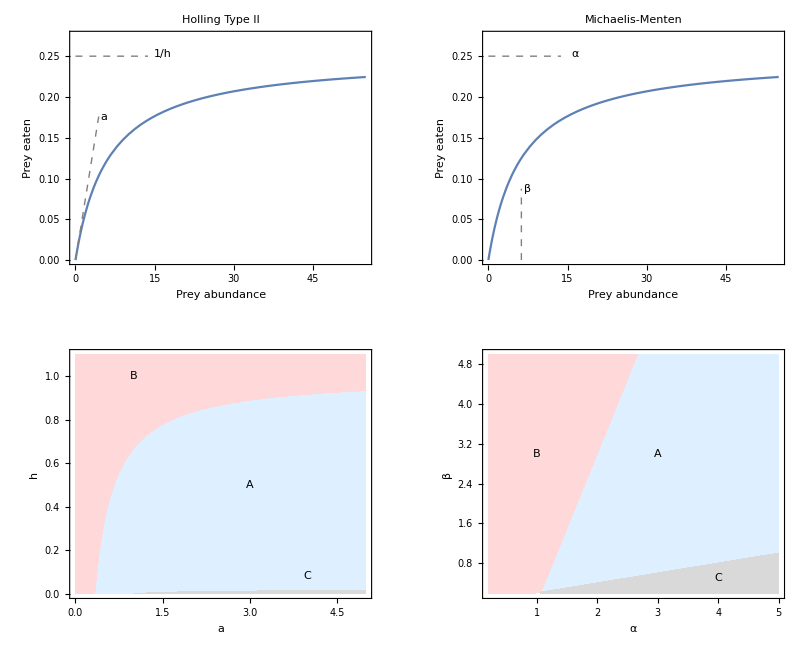

FisherInf_H2vMM.pdf

```mathematica
parmsH2= {a-> 0.04, h-> 4};
parmsMM = {α -> 1/h, β -> 1/(a h)}/.parmsH2;
parms=Join[parmsH2,parmsMM];

frH2=Plot[H2/.parms/.subs,{Ν,0,Max[Νvals]}, 
PlotRange->{0,1.1*(1/h)/.parms},
Frame-> True,
FrameLabel->{"Prey abundance","Prey eaten"},
PlotLabel->"Holling Type II"];

frMM=Plot[MM/.parms/.subs,{Ν,0,Max[Νvals]},
 PlotRange->{0,1.1*(1/h)/.parms},
Frame-> True,
FrameLabel->{"Prey abundance","Prey eaten"},
PlotLabel->"Michaelis-Menten"];

ascale = 0.08*Max[Νvals];
hscale=0.25*Max[Νvals];

aText=Text["a",{ascale*1.2,a*ascale/.parms}];
hText=Text["1/h",{hscale*1.2,1.01*1/h/.parms}];
αText=Text["α",{hscale*1.2,1.01*α/.parms}];
βText=Text["β",{1.2*β/.parms,0.35*α/.parms}];

pfrH2=Show[frH2,
Graphics[{Dashed,Gray,
Line[{{0,0},{ascale,a * ascale/.parms}}]}],
Graphics[{Dashed,Gray,
Line[{{0,1/h}/.parms,{hscale,1/h}/.parms}]}],
Graphics[aText],
Graphics[hText]
];

pfrMM=Show[frMM,
Graphics[{Dashed,Gray,
Line[{{β/.parms,0},{β/.parms,0.35*α/.parms}}]}],
Graphics[{Dashed,Gray,
Line[{{0,α}/.parms,{hscale,α}/.parms}]}],
Graphics[βText],
Graphics[αText]
];

amax = 5;
hmax = 1.1;

pRegH2=RegionPlot[
{
Callout[
a<amax && 
h < hmax && 
Max[H2/.subs/.{Ν-> Νvals}] ≤  Max[Νvals]&&
Min[H2/.subs/.{Ν-> Νvals}] ≥ 1,
"A",{3,0.5},Appearance->"None"],

Callout[
a<amax && 
h < hmax && 
Max[H2/.subs/.{Ν-> Νvals}] ≤  Max[Νvals]&&
Min[H2/.subs/.{Ν-> Νvals}] < 1,
"B",{1,1},Appearance->"None"],

Callout[
a<amax && 
h < hmax && 
Max[H2/.subs/.{Ν-> Νvals}] >  Max[Νvals]&&
Min[H2/.subs/.{Ν-> Νvals}] ≥ 1,
"C",{4,0.05},Appearance->"None"]
},
{a,0,amax},{h,0,hmax},
Frame-> True,
FrameLabel->Automatic,
BoundaryStyle->None,
PlotRangePadding-> None,
PlotStyle->{LightBlue,LightRed,LightGray}];

pRegMM=RegionPlot[
{
Callout[
α>1/amax && 
β > 1/(amax hmax) &&  
α/amax<β && 
Max[MM/.subs/.{Ν-> Νvals}] ≤  Max[Νvals]&&
Min[MM/.subs/.{Ν-> Νvals}] ≥ 1,
"A",{3,3},Appearance->"None"],

Callout[
α>1/amax && 
β > 1/(amax hmax) &&  
α/amax<β && 
Max[MM/.subs/.{Ν-> Νvals}] ≤  Max[Νvals]&&
Min[MM/.subs/.{Ν-> Νvals}] < 1,
"B",{1,3},Appearance->"None"],

Callout[
α>1/amax && 
β > 1/(amax hmax) &&  
α/amax>β && 
Max[MM/.subs/.{Ν-> Νvals}] ≤  Max[Νvals]&&
Min[MM/.subs/.{Ν-> Νvals}] ≥ 1,
"C",{4,0.5},Appearance->"None"]
},

{α,1/amax,amax},{β,1/(amax hmax),amax},
Frame-> True,
FrameLabel->Automatic,
BoundaryStyle->None,
PlotRangePadding-> None,
PlotStyle->{LightBlue,LightRed,LightGray}];

AllPlots=GraphicsGrid[{{pfrH2,pfrMM},{pRegH2,pRegMM}}]
Export["FisherInf_H2vMM.pdf",AllPlots]
```